```mathematica
Exit
```

## Old

```mathematica
a=.
b=.
c=.
d=.
```

65.632

85.5971

70.2648

114.138

True

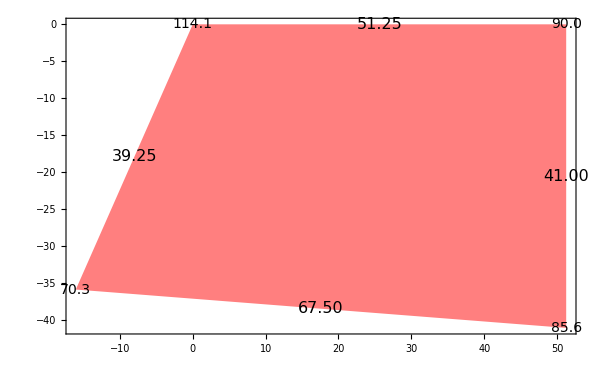

```mathematica
panel=2;
panels={{{36.5,67.5,32.5,94},{b,90 Pi/180,d,a}},{{39.25,51.25,41,67.5},{b,90 Pi/180,d,a}}};
rot=Position[panels[[panel,2]],x_?(NumberQ[#]&)][[1,1]]-1;
as=RotateLeft[panels[[panel,2]],rot];
ss=RotateLeft[panels[[panel,1]],rot];
p=√(ss[[1]]^2+ss[[2]]^2-2ss[[1]]ss[[2]]Cos[as[[1]]])
(as[[2]]=ArcCos[(-ss[[1]]^2+ss[[2]]^2+p^2)/(2 ss[[2]] p)]+ArcCos[(ss[[3]]^2-ss[[4]]^2+p^2)/(2 ss[[3]] p)])180/Pi
(as[[3]]=ArcCos[(-p^2+ ss[[3]]^2+ ss[[4]]^2)/(2 ss[[3]]ss[[4]])])180/Pi
(as[[4]]=2Pi-as[[2]]-as[[3]]-as[[1]])180/Pi
k=1/2 ss[[1]]ss[[4]]Sin[as[[4]]]+1/2 ss[[2]]ss[[3]]Sin[as[[2]]];
x={0,0,0,0};
y={0,0,0,0};
ang=-0 Pi/180;
x[[2]]=x[[1]]+ss[[1]]Sin[Pi/2-ang];
y[[2]]=y[[1]]+ss[[1]]Cos[Pi/2-ang];
x[[3]]=x[[2]]+ss[[2]]Sin[Pi/2-ang+as[[1]]];
y[[3]]=y[[2]]+ss[[2]]Cos[Pi/2-ang+as[[1]]];
x[[4]]=x[[3]]+ss[[3]]Sin[Pi/2-ang-as[[1]]-as[[2]]];
y[[4]]=y[[3]]+ss[[3]]Cos[Pi/2-ang-as[[1]]-as[[2]]];
ss==√((x-RotateLeft[x])^2+(y-RotateLeft[y])^2)
graphics2=Graphics[{Red,Opacity[0.5],Polygon[Table[{x[[i]],y[[i]]},{i,4}]],Black,Opacity[1],Table[Text[Style[ToString[NumberForm[(RotateRight[as][[i]])/Pi 180.,{4,1}]],FontSize->14],{x[[i]],y[[i]]}],{i,4}],Table[Text[Style[ToString[NumberForm[ss[[i]],{4,2}]],FontSize->16],{x[[i]]-(x[[i]]-RotateLeft[x][[i]])/2,y[[i]]-(y[[i]]-RotateLeft[y][[i]])/2}],{i,4}]},Frame->True,ImageSize->600]
```

```mathematica
(.7lbs)/(ft^2*(.125)/12 ft)*kg/(2.2lbs)((3.3ft)/m)^3(*density of polycarbonate*)
4 8 25 .7+(3 28+2 6) 2.4+(10 10+2 4+6) 1.2(*total weight of plastic and strut*)
```

(1097.71 kg)/m^3

927.2

```mathematica
botlen=0.5(94+41.25+86)+0.5(93.5+40.5+84.5)
midlen=0.5(67.5+41.75+76)+0.5(67+42+73.5)
midtoplen=0.5(51.25+42.5+56.5)+0.5(52+42.5+52.25)
toplen=(64+41.75+43.5)
posa2=36.5
pposa3=midposa+39.25
pos4=midposa+36.75
posa5
midposb=
```

219.875

183.875

148.5

149.25

```mathematica
sides=Flatten[Map[Map[Sort[#]&,Partition[Riffle[#,RotateLeft[#]],2]]&,Partition[Map[SymbolName[#]&,Delete[{F8,A2,B2,B1,A2,A3,B3,B2,B1,B2,C2,C1,B2,B3,C3,C2,F2,A6,A5,F1,A6,F2,B7,B6,
B6,B5,A5,A6,B7,B6,C6,C7,C6,C5,B5,B6,B5,A5,A4,B4,B5,B4,C4,C5,A3,A4,B4,B3,B3,B4,C4,C3,C7,D7,D6,C6,C6,D6,D5,C5,C1,D1,D2,C2,C2,C3,D3,D2,C3,C4,D4,D3,D4,D5,C5,C4},{{17},{18},{19},{20}}]/.{F8->A1,F2->A7}],4]],1];
```

```mathematica
lens=Flatten[Map[Map[#[[1;;1]]&,Partition[Riffle[#,RotateLeft[#]],2]]&,Partition[Map[#&,Delete[{36.5,67.5,32.5,94,39.25,51.25,41,67.5,32.75,41.75,32.75,41.25,41.75,42.5,41.75,41.75,35.5,39.5,52.5,24,35.5,93.5,32.5,67,40,52,39.5,67,32.75,42,33.25,40.5,41.5,42.5,40.75,42,52,36,48,64,64,41.75,63,42.5,36.75,48,64,51.25,64,41.75,64,42.5,84.5,25.5,73.5,32.75,73.5,35.75,52.25,41.25,86,25.5,76,32.5,41,56.5,34.5,76,64,43.5,46,56.5,43.5,52.5,63,43.5},{{17},{18},{19},{20}}]],4]],1];
```

```mathematica
ys=Partition[Select[Sort[Map[{#[[1,1]],#[[1,2]],Mean[#[[;;,3]]]}&,Gather[Join[sides,lens,2],#1[[1]]==#2[[1]]&&#1[[2]]==#2[[2]]&]]],StringTake[#[[1]],1]==StringTake[#[[2]],1]&],6]
```

{{{A1,A2,36.5},{A2,A3,39.25},{A3,A4,36.75},{A4,A5,36},{A5,A6,39.5},{A6,A7,35.5}},{{B1,B2,32.625},{B2,B3,41.375},{B3,B4,64},{B4,B5,64},{B5,B6,40.375},{B6,B7,32.625}},{{C1,C2,32.625},{C2,C3,41.375},{C3,C4,64},{C4,C5,63},{C5,C6,41.375},{C6,C7,33.}},{{D1,D2,25.5},{D2,D3,34.5},{D3,D4,46},{D4,D5,43.5},{D5,D6,35.75},{D6,D7,25.5}}}

```mathematica
xs=Transpose[Partition[Select[Sort[Map[{#[[1,1]],#[[1,2]],Mean[#[[;;,3]]]}&,Gather[Join[sides,lens,2],#1[[1]]==#2[[1]]&&#1[[2]]==#2[[2]]&]]],(ToCharacterCode[StringTake[#[[1]],1]]==(ToCharacterCode[StringTake[#[[2]],1]]-1)&)],7]]
```

{{{A1,B1,94},{B1,C1,41.25},{C1,D1,86}},{{A2,B2,67.5},{B2,C2,41.75},{C2,D2,76}},{{A3,B3,51.25},{B3,C3,42.5},{C3,D3,56.5}},{{A4,B4,48},{B4,C4,41.75},{C4,D4,43.5}},{{A5,B5,52},{B5,C5,42.5},{C5,D5,52.375}},{{A6,B6,67},{B6,C6,42},{C6,D6,73.5}},{{A7,B7,93.5},{B7,C7,40.5},{C7,D7,84.5}}}

```mathematica
points=Table[{0,0},{x,4},{y,7}];
points[[;;,2;;,2]]=Table[Total[ys[[i,;;j,3]]],{i,4},{j,6}];
pointst=Transpose[points];
pointst[[;;,2;;,1]]=Table[Total[xs[[i,;;j,3]]]-0xs[[1,j,3]],{i,7},{j,3}];
points=Transpose[pointst];
points[[;;,;;,1]]=Map[#-points[[2,;;,1]]&,points[[;;,;;,1]]];
points[[;;,;;,2]]=Table[points[[;;,4,2]][[i]]-points[[;;,;;,2]][[i]],{i,4}];
```

{64,63,61,60,59,58,57,56,55,53,52,51,50,49,48,47,46,45,44,43,42,42,41,40,40,40,39,39,38,38,38,37,37,37,38,38,39,39,39,40,40,40,41,42,42,43,44,45,46,47,48,49,50,51,53,54,55,56,57,59,60,61,62,63}

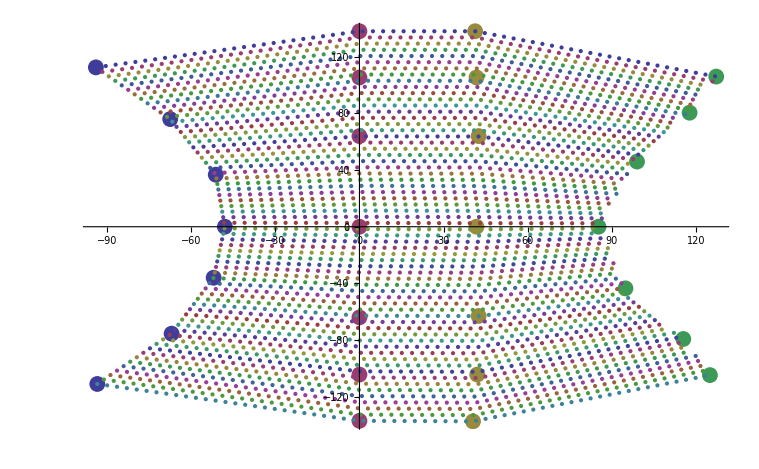

```mathematica
ydists=Map[Join[{0},Accumulate[#]]&,Table[EuclideanDistance[points[[j,i]],points[[j,i+1]]],{j,Length[points]},{i,Length[points[[1]]]-1}]];
yints=Map[Interpolation[#,InterpolationOrder->1]&,Table[{ydists[[j,i]],points[[j,i]]},{j,Length[ydists]},{i,Length[ydists[[1]]]}]];
ledpointsy=Table[yints[[i]][j],{i,Length[yints]},{j,0,ydists[[i,-1]],ydists[[i,-1]]/63}];
xdists=Map[Join[{0},Accumulate[#]]&,Table[EuclideanDistance[Transpose[ledpointsy][[j,i]],Transpose[ledpointsy][[j,i+1]]],{j,Length[Transpose[ledpointsy]]},{i,Length[Transpose[ledpointsy][[1]]]-1}]];
xints=Map[Interpolation[#,InterpolationOrder->1]&,Table[{xdists[[j,i]],Transpose[ledpointsy][[j,i]]},{j,Length[xdists]},{i,Length[xdists[[1]]]}]];
ledpoints=Table[xints[[i]][j],{i,Length[xints]},{j,0,xdists[[i,-1]],3.65}];
Map[Length[#]&,ledpoints]
Show[{ListPlot[points,PlotRange->All,PlotStyle->PointSize[.015]],ListPlot[ledpoints]}]
```

```mathematica
Sum[Sum[EuclideanDistance[ledpoints[[j,i]],ledpoints[[j,i+1]]],{i,Length[ledpoints[[j]]]-1}],{j,Length[ledpoints]}]/12/3
points
```

302.7

{{{-94,112.5},{-67.5,76.},{-51.25,36.75},{-48,0.},{-52,-36.},{-67,-75.5},{-93.5,-111.}},{{0,138.},{0.,105.375},{0.,64.},{0,0.},{0,-64.},{0,-104.375},{0.,-137.}},{{41.25,138.},{41.75,105.375},{42.5,64.},{41.75,0.},{42.5,-63.},{42.,-104.375},{40.5,-137.375}},{{127.25,106.},{117.75,80.5},{99.,46.},{85.25,0.},{94.875,-43.5},{115.5,-79.25},{125.,-104.75}}}

```mathematica
(137+138)/64//N
93/25.4*64
Sum[EuclideanDistance[ledpoints[[1,i]],ledpoints[[1,i+1]]],{i,Length[ledpoints[[1]]]-1}]
```

4.29688

234.331

229.919

```mathematica
Table["{\"point\": ["<>ToString[ledpoints[[j,i,1]]]<>", "<>ToString[ledpoints[[j,i,2]]]<>"]}",{j,Length[ledpoints]},{i,Length[ledpoints[[j]]]}]
```

```mathematica
Export["/Users/leportfr/Desktop/ledpoints.json",Table["{\"point\": ["<>ToString[ledpoints[[j,i,1]]]<>", "<>ToString[ledpoints[[j,i,2]]]<>"]}",{j,Length[ledpoints]},{i,Length[ledpoints[[j]]]}],"Table"]
```

/Users/leportfr/Desktop/ledpoints.json

```mathematica
Join[{{"LEDs","Number of strips"}},Table[{i,Count[Join[Map[Length[#]&,ledpoints],Table[64,{i,11}]],i]},{i,37,64}]]//TableForm
```

LEDs | Number of strips
37 | 3
38 | 5
39 | 5
40 | 6
41 | 2
42 | 4
43 | 2
44 | 2
45 | 2
46 | 2
47 | 2
48 | 2
49 | 2
50 | 2
51 | 2
52 | 1
53 | 2
54 | 1
55 | 2
56 | 2
57 | 2
58 | 1
59 | 2
60 | 2
61 | 2
62 | 1
63 | 2
64 | 12

```mathematica
Table[{i,Count[Join[Map[Length[#]&,ledpoints],Table[64,{i,11}]],i]},{i,37,64}]
Total[Flatten[Table[{i*Count[Join[Map[Length[#]&,ledpoints],Table[64,{i,11}]],i]},{i,37,64}]]]
```

{{37,3},{38,5},{39,5},{40,6},{41,2},{42,4},{43,2},{44,2},{45,2},{46,2},{47,2},{48,2},{49,2},{50,2},{51,2},{52,1},{53,2},{54,1},{55,2},{56,2},{57,2},{58,1},{59,2},{60,2},{61,2},{62,1},{63,2},{64,12}}

3754

```mathematica
3754 .045 5/2+4 250+200+850
```

2472.33

```mathematica
Total[Table[Length[ledpoints[[i]]],{i,24}]].06//N
Total[Table[Length[ledpoints[[i]]],{i,25,48}]].06+4 64 .06//N
Total[Table[Length[ledpoints[[i]]],{i,49,64}]].06+4 64 .06//N
```

73.56

72.54

67.62

```mathematica
Total[Table[Length[ledpoints[[i]]],{i,8}]].06//N
```

28.68

```mathematica
17.99 30
18.99 24+{258.31,303.31}
```

539.7

{714.07,759.07}

```mathematica
775 624 8839
```

```mathematica
Map[Total[#]&,Partition[Map[Length[#]&,ledpoints],8]]
64 4
```

{478,405,343,309,307,337,398,473}

256

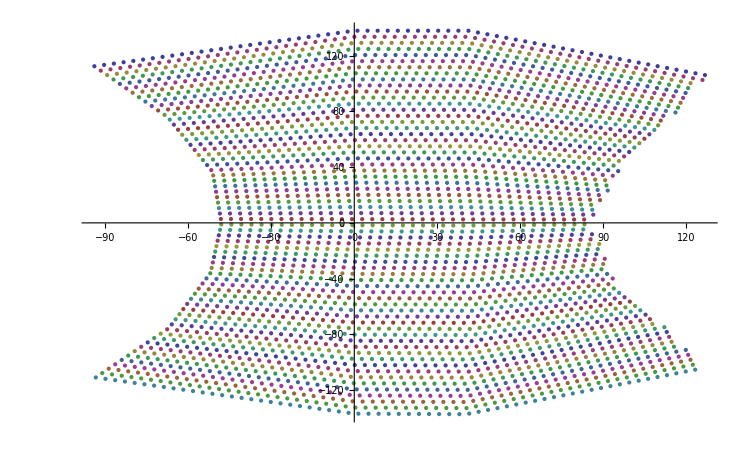

```mathematica
ListPlot[ledpoints]
```

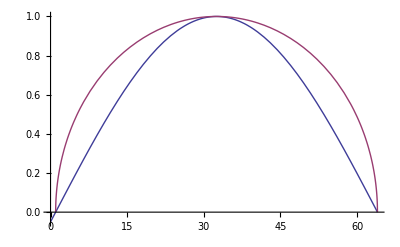

```mathematica
Plot[{Sin[(i-1)/31.5 Pi/2],√(1-((i-1-31.5)/31.5)^2)},{i,0,64}]
```

```mathematica
ledpointsz=Table[0,{i,64}];
zs=Table[{6,0,0,6}+{7 12,10 12,10 12,7 12}√(1-((i-1-31.5)/31.5)^2),{i,64}]//N
Do[
p1=Count[ledpoints[[strip]],x_?(#[[1]]<0&)];
p2=Count[ledpoints[[strip]],x_?(#[[1]]>42&)];
zd1=(zs[[strip,2]]-zs[[strip,1]])/(p1-1);
zd2=(zs[[strip,4]]-zs[[strip,3]])/(p2-1);
ledpointsz[[strip]]=Join[ledpoints[[strip]],Join[Table[{zs[[strip,1]]+zd1 (i-1)},{i,p1}],Table[{zs[[strip,2]]},{i,Length[ledpoints[[strip]]]-p1-p2}],Table[{zs[[strip,3]]+zd2 (i-1)},{i,p2}]],2];,{strip,1,64}]
```

{{6.,0.,0.,6.},{26.9974,29.9962,29.9962,26.9974},{35.4543,42.0776,42.0776,35.4543},{41.7771,51.1101,51.1101,41.7771},{46.9661,58.523,58.523,46.9661},{51.4117,64.8739,64.8739,51.4117},{55.3153,70.4504,70.4504,55.3153},{58.7973,75.4247,75.4247,58.7973},{61.9365,79.9092,79.9092,61.9365},{64.7878,83.9825,83.9825,64.7878},{67.3913,87.7018,87.7018,67.3913},{69.7774,91.1106,91.1106,69.7774},{71.9697,94.2424,94.2424,71.9697},{73.9869,97.1242,97.1242,73.9869},{75.8443,99.7775,99.7775,75.8443},{77.5542,102.22,102.22,77.5542},{79.127,104.467,104.467,79.127},{80.5714,106.531,106.531,80.5714},{81.8947,108.421,108.421,81.8947},{83.1031,110.147,110.147,83.1031},{84.202,111.717,111.717,84.202},{85.196,113.137,113.137,85.196},{86.0888,114.413,114.413,86.0888},{86.884,115.549,115.549,86.884},{87.5843,116.549,116.549,87.5843},{88.1922,117.417,117.417,88.1922},{88.7097,118.157,118.157,88.7097},{89.1384,118.769,118.769,89.1384},{89.4799,119.257,119.257,89.4799},{89.735,119.621,119.621,89.735},{89.9047,119.864,119.864,89.9047},{89.9894,119.985,119.985,89.9894},{89.9894,119.985,119.985,89.9894},{89.9047,119.864,119.864,89.9047},{89.735,119.621,119.621,89.735},{89.4799,119.257,119.257,89.4799},{89.1384,118.769,118.769,89.1384},{88.7097,118.157,118.157,88.7097},{88.1922,117.417,117.417,88.1922},{87.5843,116.549,116.549,87.5843},{86.884,115.549,115.549,86.884},{86.0888,114.413,114.413,86.0888},{85.196,113.137,113.137,85.196},{84.202,111.717,111.717,84.202},{83.1031,110.147,110.147,83.1031},{81.8947,108.421,108.421,81.8947},{80.5714,106.531,106.531,80.5714},{79.127,104.467,104.467,79.127},{77.5542,102.22,102.22,77.5542},{75.8443,99.7775,99.7775,75.8443},{73.9869,97.1242,97.1242,73.9869},{71.9697,94.2424,94.2424,71.9697},{69.7774,91.1106,91.1106,69.7774},{67.3913,87.7018,87.7018,67.3913},{64.7878,83.9825,83.9825,64.7878},{61.9365,79.9092,79.9092,61.9365},{58.7973,75.4247,75.4247,58.7973},{55.3153,70.4504,70.4504,55.3153},{51.4117,64.8739,64.8739,51.4117},{46.9661,58.523,58.523,46.9661},{41.7771,51.1101,51.1101,41.7771},{35.4543,42.0776,42.0776,35.4543},{26.9974,29.9962,29.9962,26.9974},{6.,0.,0.,6.}}

```mathematica
ListPointPlot3D[Flatten[ledpointsz,1],AspectRatio->1,PlotRange->{{-180,180},{-180,180},{-180,180}}]
```

-Graphics3D-

## 3D Points

```mathematica
rmh=12 9;
rmw=12 12/2;
yd=42;
fd=12 √(7.5^2-2.5^2);
rfh=12 7;
rfr=12 7.75;
rfw=12 7/2;
fang=60;
mz=-12;
striplens=Table[{If[i<10,Floor[i/1.66],If[i>53,Floor[(63-i)/1.66],0]],64-3-If[i<10,Floor[i/1.66],If[i>53,Floor[(63-i)/1.66],8]]-Ceiling[(32-Abs[32-i])20/37]},{i,0,63}]
ledpoints3d={Table[{rfw Cos[i/63 Pi],-fd+rfh Sin[i/63 Pi]Sin[(90-fang) Pi/180],rfh Sin[i/63 Pi]Cos[(90-fang) Pi/180]},{i,0,63}],Table[{rmw Cos[i/63 Pi],0,rmh Sin[i/63 Pi]+mz},{i,0,63}],
Table[{rmw Cos[i/63 Pi],yd,rmh Sin[i/63 Pi]+mz},{i,0,63}],
Table[{rfw Cos[i/63 Pi],yd+fd-rfr Sin[i/63 Pi]Sin[(90-fang) Pi/180],rfr Sin[i/63 Pi]Cos[(90-fang) Pi/180]},{i,0,63}]}//Transpose//N;
stripdists=Map[Join[{0},Accumulate[#]]&,Table[EuclideanDistance[ledpoints3d[[j,i]],ledpoints3d[[j,i+1]]],{j,Length[ledpoints3d]},{i,Length[ledpoints3d[[1]]]-1}]];
stripints=Map[Interpolation[#,InterpolationOrder->1]&,Table[{stripdists[[j,i]],ledpoints3d[[j,i]]},{j,Length[stripdists]},{i,Length[stripdists[[1]]]}]];
ledpoints3dstrips=Table[stripints[[i]][j],{i,Length[stripints]},{j,-striplens[[i,1]] stripdists[[i,-1]]/striplens[[i,2]],stripdists[[i,-1]],stripdists[[i,-1]]/striplens[[i,2]]}];
imagesize3d=150;
ListPointPlot3D[ledpoints3dstrips
,PlotRange->{{-imagesize3d,imagesize3d},{-imagesize3d,imagesize3d},{-imagesize3d,imagesize3d}},AspectRatio->1]
```

{{0,61},{0,60},{1,58},{1,58},{2,56},{3,55},{3,54},{4,53},{4,52},{5,51},{0,47},{0,47},{0,46},{0,45},{0,45},{0,44},{0,44},{0,43},{0,43},{0,42},{0,42},{0,41},{0,41},{0,40},{0,40},{0,39},{0,38},{0,38},{0,37},{0,37},{0,36},{0,36},{0,35},{0,36},{0,36},{0,37},{0,37},{0,38},{0,38},{0,39},{0,40},{0,40},{0,41},{0,41},{0,42},{0,42},{0,43},{0,43},{0,44},{0,44},{0,45},{0,45},{0,46},{0,47},{5,50},{4,52},{4,52},{3,54},{3,54},{2,56},{1,57},{1,58},{0,59},{0,60}}

InterpolatingFunction::dmval: Input value {-3.69882} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.62117} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.34132} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics3D-

3.64198

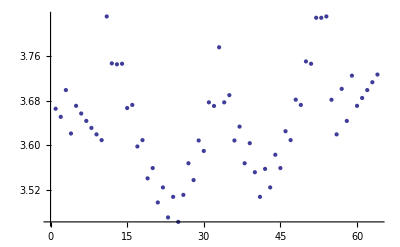

3030

```mathematica
Table[EuclideanDistance[ledpoints3dstrips[[i,1]],ledpoints3dstrips[[i,1+1]]],{i,Length[ledpoints3dstrips]}]//Mean
ListPlot[Table[EuclideanDistance[ledpoints3dstrips[[i,1]],ledpoints3dstrips[[i,1+1]]],{i,Length[ledpoints3dstrips]}]]
Flatten[ledpoints3dstrips,1]//Length
```

```mathematica
ledpoints3d[[32,2,3]]-ledpoints3d[[32,1,3]]//N
ledpoints3d[[32,3,3]]-ledpoints3d[[32,4,3]]//N
EuclideanDistance[ledpoints3d[[1,1]],ledpoints3d[[1,2]]]/12
EuclideanDistance[ledpoints3d[[1,3]],ledpoints3d[[1,4]]]/12
```

23.2429

15.4511

7.56637

7.56637

```mathematica
ledpoints3dstrips[[;;10,1,2]]
```

{-84.8528,-82.7593,-84.1231,-81.97,-83.3708,-84.7002,-82.6356,-83.974,-81.9625,-83.3353}

```mathematica
Map[Join[{0},Accumulate[#]]&,Table[EuclideanDistance[Transpose[ledpoints3d][[j,i]],Transpose[ledpoints3d][[j,i+1]]],{j,Length[Transpose[ledpoints3d]]},{i,Length[Transpose[ledpoints3d][[1]]]-1}]][[;;,-1]]//N
```

{203.436,285.548,285.548,219.671}

```mathematica
Export[NotebookDirectory[]<>"LEDPoints.csv",Join[Select[Flatten[ledpoints3dstrips,1],#[[1]]>0&],Select[Flatten[ledpoints3dstrips,1],#[[1]]<0&]],"CSV"]
Export[NotebookDirectory[]<>"ShellStripLens.csv",striplens,"CSV"]
```

/Users/leportfr/Desktop/Lovebug/LEDs/LoveBug/LEDPoints.csv

/Users/leportfr/Desktop/Lovebug/LEDs/LoveBug/ShellStripLens.csv

## 2 D Points

```mathematica
height=1080*2/3-1;
width=1920*2/3;
```

```mathematica
sides=Flatten[Map[Map[Sort[#]&,Partition[Riffle[#,RotateLeft[#]],2]]&,Partition[Map[SymbolName[#]&,Delete[{F8,A2,B2,B1,A2,A3,B3,B2,B1,B2,C2,C1,B2,B3,C3,C2,F2,A6,A5,F1,A6,F2,B7,B6,
B6,B5,A5,A6,B7,B6,C6,C7,C6,C5,B5,B6,B5,A5,A4,B4,B5,B4,C4,C5,A3,A4,B4,B3,B3,B4,C4,C3,C7,D7,D6,C6,C6,D6,D5,C5,C1,D1,D2,C2,C2,C3,D3,D2,C3,C4,D4,D3,D4,D5,C5,C4},{{17},{18},{19},{20}}]/.{F8->A1,F2->A7}],4]],1];
```

```mathematica
lens=Flatten[Map[Map[#[[1;;1]]&,Partition[Riffle[#,RotateLeft[#]],2]]&,Partition[Map[#&,Delete[{36.5,67.5,32.5,94,39.25,51.25,41,67.5,32.75,41.75,32.75,41.25,41.75,42.5,41.75,41.75,35.5,39.5,52.5,24,35.5,93.5,32.5,67,40,52,39.5,67,32.75,42,33.25,40.5,41.5,42.5,40.75,42,52,36,48,64,64,41.75,63,42.5,36.75,48,64,51.25,64,41.75,64,42.5,84.5,25.5,73.5,32.75,73.5,35.75,52.25,41.25,86,25.5,76,32.5,41,56.5,34.5,76,64,43.5,46,56.5,43.5,52.5,63,43.5},{{17},{18},{19},{20}}]],4]],1];
```

```mathematica
ys=Partition[Select[Sort[Map[{#[[1,1]],#[[1,2]],Mean[#[[;;,3]]]}&,Gather[Join[sides,lens,2],#1[[1]]==#2[[1]]&&#1[[2]]==#2[[2]]&]]],StringTake[#[[1]],1]==StringTake[#[[2]],1]&],6]
```

{{{A1,A2,36.5},{A2,A3,39.25},{A3,A4,36.75},{A4,A5,36},{A5,A6,39.5},{A6,A7,35.5}},{{B1,B2,32.625},{B2,B3,41.375},{B3,B4,64},{B4,B5,64},{B5,B6,40.375},{B6,B7,32.625}},{{C1,C2,32.625},{C2,C3,41.375},{C3,C4,64},{C4,C5,63},{C5,C6,41.375},{C6,C7,33.}},{{D1,D2,25.5},{D2,D3,34.5},{D3,D4,46},{D4,D5,43.5},{D5,D6,35.75},{D6,D7,25.5}}}

```mathematica
xs=Transpose[Partition[Select[Sort[Map[{#[[1,1]],#[[1,2]],Mean[#[[;;,3]]]}&,Gather[Join[sides,lens,2],#1[[1]]==#2[[1]]&&#1[[2]]==#2[[2]]&]]],(ToCharacterCode[StringTake[#[[1]],1]]==(ToCharacterCode[StringTake[#[[2]],1]]-1)&)],7]]
```

{{{A1,B1,94},{B1,C1,41.25},{C1,D1,86}},{{A2,B2,67.5},{B2,C2,41.75},{C2,D2,76}},{{A3,B3,51.25},{B3,C3,42.5},{C3,D3,56.5}},{{A4,B4,48},{B4,C4,41.75},{C4,D4,43.5}},{{A5,B5,52},{B5,C5,42.5},{C5,D5,52.375}},{{A6,B6,67},{B6,C6,42},{C6,D6,73.5}},{{A7,B7,93.5},{B7,C7,40.5},{C7,D7,84.5}}}

```mathematica
points=Table[{0,0},{x,4},{y,7}];
points[[;;,2;;,2]]=Table[Total[ys[[i,;;j,3]]],{i,4},{j,6}];
pointst=Transpose[points];
pointst[[;;,2;;,1]]=Table[Total[xs[[i,;;j,3]]]-0xs[[1,j,3]],{i,7},{j,3}];
points=Transpose[pointst];
points[[;;,;;,1]]=Map[#-points[[2,;;,1]]&,points[[;;,;;,1]]];
points[[;;,;;,2]]=Table[points[[;;,4,2]][[i]]-points[[;;,;;,2]][[i]],{i,4}];
```

InterpolatingFunction::dmval: Input value {-3.8328} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.76308} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.65077} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

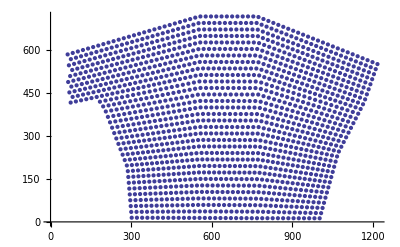

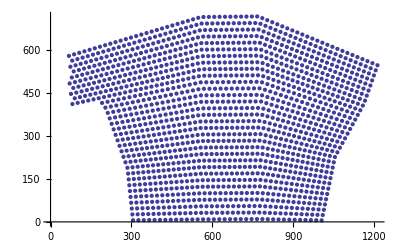

```mathematica
ydists=Map[Join[{0},Accumulate[#]]&,Table[EuclideanDistance[points[[j,i]],points[[j,i+1]]],{j,Length[points]},{i,Length[points[[1]]]-1}]];
yints=Map[Interpolation[#,InterpolationOrder->1]&,Table[{ydists[[j,i]],points[[j,i]]},{j,Length[ydists]},{i,Length[ydists[[1]]]}]];
ledpointsy=Table[yints[[i]][j],{i,Length[yints]},{j,0,ydists[[i,-1]],ydists[[i,-1]]/63}];
xdists=Map[Join[{0},Accumulate[#]]&,Table[EuclideanDistance[Transpose[ledpointsy][[j,i]],Transpose[ledpointsy][[j,i+1]]],{j,Length[Transpose[ledpointsy]]},{i,Length[Transpose[ledpointsy][[1]]]-1}]];
xints=Map[Interpolation[#,InterpolationOrder->1]&,Table[{xdists[[j,i]],Transpose[ledpointsy][[j,i]]},{j,Length[xdists]},{i,Length[xdists[[1]]]}]];
ledpoints=Table[xints[[i]][j],{i,Length[xints]},{j,-striplens[[i,1]] xdists[[i,-1]]/striplens[[i,2]],xdists[[i,-1]],xdists[[i,-1]]/striplens[[i,2]]}];
half=Select[Flatten[ledpoints,1],#[[2]]>0&];
half2=Select[Flatten[ledpoints,1],#[[2]]<0&];
ListPlot[Map[{width/2+(#[[1]]-(Max[half[[;;,1]]]+Min[half[[;;,1]]])/2)*height/Max[half[[;;,2]]],#[[2]]*height/Max[half[[;;,2]]]}&,half]]
ListPlot[Map[{width/2+(#[[1]]-(Max[half2[[;;,1]]]+Min[half2[[;;,1]]])/2)*height/Max[-half2[[;;,2]]],-#[[2]]*height/Max[-half2[[;;,2]]]}&,half2]]
```

```mathematica
Export[NotebookDirectory[]<>"LED2DPoints.csv",Map[Round[width/2+(#[[1]]-(Max[half[[;;,1]]]+Min[half[[;;,1]]])/2)*height/Max[half[[;;,2]]]]+width Round[#[[2]]*height/Max[half[[;;,2]]]]&,half],"CSV"]
Export[NotebookDirectory[]<>"LED2DPoints2.csv",Map[Round[width/2+(#[[1]]-(Max[half2[[;;,1]]]+Min[half2[[;;,1]]])/2)*height/Max[-half2[[;;,2]]]]+width Round[-#[[2]]*height/Max[-half2[[;;,2]]]]&,half2],"CSV"]
```

/Users/leportfr/Desktop/Lovebug/LEDs/LoveBug/LED2DPoints.csv

/Users/leportfr/Desktop/Lovebug/LEDs/LoveBug/LED2DPoints2.csv

```mathematica
Length[half]
Length[half2]
Flatten[ledpoints3dstrips,1]//Length
```

1524

1506

3030

## Backflap

```mathematica
ldist=3.65;
4+11ldist
```

44.15

```mathematica
a=42-7;
h=87.5-49;
a=.;
h=.;
(√(a^2+4 h^2)+a^2/(2h)ArcSinh[(2h)/a])/(2 ldist)
y==h(1-x^2/a^2)//FullSimplify
```

0.136986 (√(a^2+4 h^2)+(a^2 ArcSinh[(2 h)/a])/(2 h))

(h x^2)/a^2+y==h

```mathematica
line3=Table[{7,87.5}+{a,-a^2 0.03142857142857143}/.NSolve[{0.13698 (√(a^2+0.0039508 a^4)+15.9093 ArcSinh[0.062856 a])==i,a≥0},a,Reals][[1]],{i,0,15}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

{{7.,87.5},{10.6192,87.0883},{14.0738,85.9274},{17.2753,84.1817},{20.2104,82.0153},{22.9025,79.5521},{25.3849,76.877},{27.6895,74.0469},{29.8432,71.1002},{31.8683,68.0635},{33.7828,64.9557},{35.6011,61.7907},{37.3351,58.5788},{38.9947,55.3277},{40.5881,52.0436},{42.1219,48.7313}}

```mathematica
backflap=Join[Table[{3.5,88}-{0,ldist}(i-1),{i,24}],
Table[{4,0}+{ldist,0}(i-1),{i,12}],
Table[{46,2}+{0,ldist}(i-1),{i,2}],
Table[{45,7}-{ldist,0}(i-1),{i,10}],
Table[{10.5,8.5}+{0,ldist}(i-1),{i,2}],
Table[{12.5,14}+{ldist,0}(i-1),{i,10}],
Table[{10.5,87}-{0,ldist}(i-1),{i,18}],
Table[{12,21}+{ldist,0}(i-1),{i,10}],
Table[{46,23}+{0,ldist}(i-1),{i,2}],
Table[{44,28}-{ldist,0}(i-1),{i,8}],
Table[{17.5,30}+{0,ldist}(i-1),{i,2}],
Table[{19,35}+{ldist,0}(i-1),{i,8}],
Table[{44.5,36}+{0,ldist}(i-1),{i,2}],
Table[{42,42}-{ldist,0}(i-1),{i,8}],
Table[{14,41}-{0,ldist}(i-1),{i,5}],
Table[{16,24.4}-{0,ldist}(i-1),{i,1}],
line3,
Table[{40,49}-{ldist,0}(i-1),{i,7}],
Table[{17,51}+{0,ldist}(i-1),{i,2}],
Table[{18,56}+{ldist,0}(i-1),{i,5}],
Table[{33,57.5}+{-√(2ldist),√(2ldist)}(i-1),{i,3}],
Table[{27.5-ldist,63}-{ldist,0}(i-1),{i,3}],
Table[{17,65}+{0,ldist}(i-1),{i,2}],
Table[{18,70}+{ldist,0}(i-1),{i,3}],
Table[{25,71}+{-√(2ldist),√(2ldist)}(i-1),{i,4}],
Table[{14,78}-{0,ldist}(i-1),{i,9}],
Table[{16,45.5}+{ldist,0}(i-1),{i,8}]
];
```

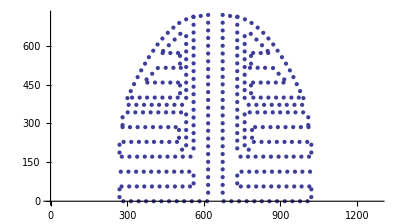

```mathematica
backflap2d=Map[Round[{width/2+Max[backflap[[;;,1]]]/(height/Max[backflap[[;;,2]]])+#[[1]],#[[2]]}]&,height/Max[backflap[[;;,2]]] Join[backflap,Map[#*{-1,1}&,backflap]]];
ListPlot[backflap2d,PlotRange->{{0,width},{0,height}},AspectRatio->height/width]
```

```mathematica
Export[NotebookDirectory[]<>"BackFlap2D.csv",Map[#[[1]]+width(height-#[[2]])&,backflap2d],"CSV"]
```

/Users/leportfr/Desktop/Lovebug/LEDs/LoveBug/BackFlap2D.csv

```mathematica
backflap3d=Join[Map[{.85#[[1]],yd+fd-#[[2]]Cos[fang Pi/180],#[[2]]Sin[fang Pi/180]+2}&,backflap],
Map[{-.85#[[1]],yd+fd-#[[2]]Cos[fang Pi/180],#[[2]]Sin[fang Pi/180]+2}&,backflap]]//N;
ListPointPlot3D[Join[Flatten[ledpoints3dstrips,1],backflap3d]
,PlotRange->{{-imagesize3d,imagesize3d},{-imagesize3d,imagesize3d},{-imagesize3d,imagesize3d}},AspectRatio->1]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"BackFlap.csv",backflap3d,"CSV"]
```

/Users/leportfr/Desktop/Lovebug/LEDs/LoveBug/BackFlap.csv